```mathematica
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\FORM.m"]
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[vars_,ov_,ec_,rs_]:=Block[{Po,siga,sigy,pi,d,t,young,nu,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

{siga,sigy,pi,d,t,young,nu}=vars;

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

initialguess=pi+deltaptresca;

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

(*Print["deltapy = ",deltapy];*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
(*H=0.22;*)
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{Po,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

(*initialguess=pi+deltaptresca;*)

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.0001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},

{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}(*/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}*)
]
```

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{a,kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
If[Abs[sa]<fu,a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)),a=0];
pfactorNeck=Sqrt[a];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

```mathematica
ComputeNumericalGradKS[Vars_,Xvec_]:=Block[{n,de,t,fu,sa,pi,po,i,derivative,xvecn1,dgdx,dx=0.001,xvecn,NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
{n,de,t,fu,sa,pi,po}=Vars;
xvecn=Xvec;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:= xvec[[1]]*ComputeBurstResistance[n,de,xvec[[3]]*t,xvec[[2]]*fu,xvec[[4]]*sa,xvec[[5]]*po]-xvec[[6]] pi;

derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

# -Graphics-

```mathematica
checkconv[vars_,pt_,GxGradx_]:=Block[{nsz=10,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate},
diffnorm=Table[0,{nsz}];
referenceresidual=GxGradx[vars,pt][[1]];
tan=GxGradx[vars,pt][[2]] ;
numrows=Length[pt];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range=pt/197;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];
Print["tan = ",tan];
Print["incval = ",incval];
estimateresidual=tan .incval;
Print["estimateresidual = ",estimateresidual];
For[i=1,i<nsz,i++,
actualstate=pt;
For[k=1,k≤numrows,k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
res=GxGradx[vars,actualstate][[1]];
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

72.7598

57.2133

15.5465

5000-po+9481.26 √(1.-8.84348×10^-13 (24863.3+72.7598 po)^2)

MisesEq[5000,po,9.625,0.545,20000,80000,0.855]

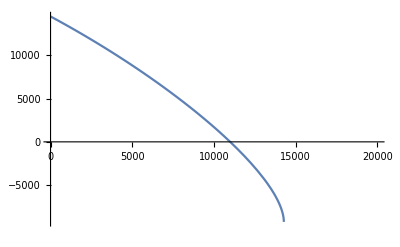

{po→10988.7}

5988.72

```mathematica
(*exemplo pagina 194 ISO 10400*)
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
feff=siga As -pi Ai+po Ao;
deltapmises=Sqrt[(ky(4./√3.)sigy t/(de-t))^2 (1.-(feff/(ky sigy As))^2)]-po+pi
MisesEq[pi,po,de,t,siga,sigy,ky]
Plot[{deltapmises,MisesEq[pi,po,de,t,siga,sigy,ky]},{po,0,20000}]
sol1=FindRoot[deltapmises,{po,10000}]
sol1[[1,2]]-pi
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKTOld[vars_,ov_,ec_,rs_]:=Block[{siga,sigy,pi,d,t,young,nu,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
{siga,sigy,pi,d,t,young,nu}=vars;
deltaptresca=ky 2 sigy t/(d-t);
deltapmises= Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
(*Print["deltapmises = ",deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=0.22;
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
di=5.795;
de=7;
t=(de-di)/2;
ov=0.217;
ex=3.924;
rs=-0.237;
sigy=125000;
area=Pi/4(de^2-di^2)
Lvec={0,100,1480,2960,4440,5920,7400,8880,9066,10360,11840,13320,13885,14800};
PI={0.00,0.05,0.77,1.54,2.31,3.08,3.84,4.61,4.71,5.38,6.15,6.92,7.21,7.74};
PE={0.09,90.91,1345.45,2690.91,4036.36,5381.81,6727.27,8072.72,8241.81,9418.17,10763.62,12109.07,12622.71,13454.44};
DeltaP=PE-PI;
DeltaP=Table[{DeltaP[[i]],-Lvec[[i]]},{i,1,Length[DeltaP]}];
FA={303906,300110,247670,191430,135190,78950,22710,-33530,-40598,-89770,-146010,-202250,-223720,-258490};
Length[PI]
Length[PE]
Length[Lvec]
Length[FA]

KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
M=Transpose[KTRandomVarsData][[3]]
SDev=Transpose[KTRandomVarsData][[4]]
distr=Transpose[KTRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
ov=0.217;
ex=3.924;
rs=-0.237;
sigy=95000;
area=Pi/4(de^2-di^2);
vars=Table[{FA[[i]]/area,sigy,PI[[i]],PE[[i]],de,t,3 10^7,0.3},{i,1,Length[FA]}];
```

12.1092

14

14

14

«1 more identical outputs»

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

{0.9991,1.1,1.0069,0.217,3.924,-0.237,1.,1.,1.}

{0.0669397,0.04642,0.0260787,0.117397,2.59376,0.078684,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

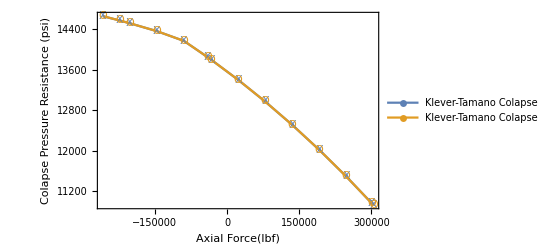

```mathematica
graphtamano=Table[{FA[[i]],ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[PI]}];
graphtamanoold=Table[{FA[[i]],ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[PI]}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Axial Force(lbf)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotMarkers->{"X","O"}]
```

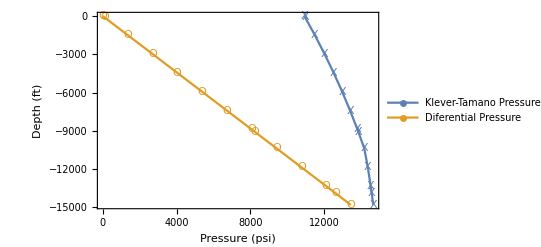

```mathematica
graphtamano=Table[{ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs],-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{graphtamano,DeltaP},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)",""}},PlotLegends->{"Klever-Tamano Pressure Resistance","Diferential Pressure"},PlotMarkers->{"X","O"}]
```

```mathematica
Table[checkconv[vars[[i]],M,ComputeNumericalGradKT],{i,1,3}]
```

tan = {12345.5,13120.4,14382.5,-560.877,-17.224,1943.29,-3014.76,0.,-0.09}

incval = {0.00263989,0.00525234,0.00192967,0.0000519826,0.00269528,-0.000737282,0.00237256,0.00150363,0.00360744}

estimateresidual = 120.596

1.97067

1.98321

1.98827

1.99108

1.99288

1.99416

1.99512

1.99587

tan = {12383.1,13102.9,14439.2,-564.645,-17.3397,1956.34,-2965.19,0.0939729,-90.91}

incval = {0.00471646,0.00547993,0.00103983,0.000244263,0.00843948,-0.0000291091,0.00159578,0.00261267,0.00324606}

estimateresidual = 139.854

1.9799

1.98854

1.99201

1.99392

1.99515

1.99602

1.99667

1.99719

tan = {12888.2,12876.3,15211.3,-616.577,-18.9345,2136.28,-2314.15,1.45219,-1345.45}

incval = {0.00212475,0.0048505,0.00400034,0.000415095,0.0169494,-0.000911734,0.00343827,0.0043647,0.0000619298}

estimateresidual = 140.133

1.97406

1.98522

1.98973

1.99223

1.99386

1.99501

1.99588

1.99658

{{0.0036397,0.0142658,0.0318802,0.0564851,0.0880824,0.126674,0.172262,0.224849,0.284437,0},{0.00450374,0.0177656,0.0397874,0.0705707,0.110117,0.158429,0.215507,0.281354,0.35597,0},{0.00508394,0.0199735,0.0446718,0.0791823,0.123508,0.177653,0.241619,0.315411,0.399031,0}}

| iter = 8  | residual = 1.00289×10^-7 | G(x) = 7.30523×10^-10| Beta = 14.9253

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| iter = 8  | residual = 1.12821×10^-7 | G(x) = 2.49609×10^-9| Beta = 14.8154

| iter = 7  | residual = 8.43947×10^-6 | G(x) = -0.000146033| Beta = 13.3047

| iter = 8  | residual = 8.16629×10^-6 | G(x) = -0.00024646| Beta = 11.7213

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| iter = 8  | residual = 8.67517×10^-6 | G(x) = -0.000349454| Beta = 10.2129

| iter = 7  | residual = 0.0000441798 | G(x) = -0.00180298| Beta = 8.80426

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

| iter = 7  | residual = 9.47767×10^-6 | G(x) = -0.000318155| Beta = 7.50118

| iter = 6  | residual = 0.0000472725 | G(x) = -0.00127987| Beta = 6.29712

| iter = 6  | residual = 0.0000388607 | G(x) = -0.00101277| Beta = 6.15227

| iter = 6  | residual = 9.09728×10^-6 | G(x) = -0.000172102| Beta = 5.18099

| iter = 5  | residual = 0.0000878895 | G(x) = -0.00121346| Beta = 4.0487

| iter = 5  | residual = 0.0000123493 | G(x) = -0.0000884631| Beta = 2.97613

| iter = 5  | residual = 5.03012×10^-6 | G(x) = -0.0000239331| Beta = 2.58324

| iter = 4  | residual = 0.0000465839 | G(x) = -0.0010483| Beta = 1.96512

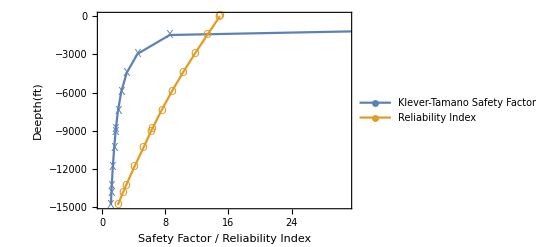

```mathematica
plotbeta=Table[{HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
SF=Table[{ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]/(PE[[i]]-PI[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{SF,plotbeta},Frame->True,FrameLabel->{{"Deepth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Klever-Tamano Safety Factor","Reliability Index"},PlotMarkers->{"X","O"}]
```

```mathematica
TableForm[PrependTo[SF,{"Safety Factor","Depth"}]]
TableForm[PrependTo[plotbeta,{"Reliability Index","Depth"}]]
```

Safety Factor | Depth
121417. | 0
120.699 | -100
8.545 | -1480
4.46866 | -2960
3.10153 | -4440
2.41193 | -5920
1.99347 | -7400
1.7107 | -8880
1.68143 | -9066
1.50551 | -10360
1.33526 | -11840
1.19977 | -13320
1.15537 | -13885
1.09033 | -14800

Reliability Index | Depth
14.9253 | 0
14.8154 | -100
13.3047 | -1480
11.7213 | -2960
10.2129 | -4440
8.80426 | -5920
7.50118 | -7400
6.29712 | -8880
6.15227 | -9066
5.18099 | -10360
4.0487 | -11840
2.97613 | -13320
2.58324 | -13885
1.96512 | -14800

```mathematica
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.01},{"Pext","NORMAL",1.0,0.01},{"Pint","NORMAL",1.0,0.01}};
```

```mathematica
M=Transpose[KSRandomVarsData][[3]]
SDev=Transpose[KSRandomVarsData][[4]]
distr=Transpose[KSRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
(*n,de,t,fu,sa,pi,po*)
vars={0.104,9.625,1.089,80000 1.15,20000,10000,0}
```

{1.004,1.1,1.0069,1.,1.,1.}

{0.047188,0.04642,0.0260787,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{1.004,0.047188,1.004,0.047188,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

{0.104,9.625,1.089,92000.,20000,10000,0}

```mathematica
ComputeNumericalGradKS[vars,M]
```

{15380.3,{25279.2,23516.8,28450.9,-488.62,0.,-10000.}}

```mathematica
Table[checkconv[vars,M,ComputeNumericalGradKS],{i,1,2}]
```

tan = {25279.2,23516.8,28450.9,-488.62,0.,-10000.}

incval = {0.00102446,0.00190223,0.00361536,0.000281336,0.00406226,0.00359152}

estimateresidual = 137.44

2.32415

2.16028

2.10785

2.08157

2.06573

2.05514

2.04756

2.04188

tan = {25279.2,23516.8,28450.9,-488.62,0.,-10000.}

incval = {0.00129012,0.00451772,0.00370513,0.000155096,0.00284218,0.00245618}

estimateresidual = 219.632

2.13557

2.07285

2.05043

2.03877

2.03162

2.0268

2.02333

2.02074

{{0.00251499,0.0125943,0.0302401,0.0554542,0.0882387,0.128596,0.176527,0.232035,0.295121,0},{0.00633993,0.0278584,0.0645605,0.116452,0.183537,0.265821,0.363309,0.476007,0.603919,0}}

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]
```

```mathematica
Lvec={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PI={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PE={0.05,311.69,623.38,935.06,1038.91,1039.01,1246.75,1558.43,1870.11,2181.79,2493.48,2805.16,3116.79,3116.89,3117.10,3233.72,3350.56,3467.39,3584.23,3701.06,3817.90,3934.74,4051.57,4168.41,4285.24,4328.52,4371.79,4415.06,4458.33,4501.61,4544.88,4588.15,4631.43,4674.70,4717.93};
FA={813678,767485,721285,675085,659693,659678,628885,582685,536485,490286,444086,397886,351686,670316,670345,685848,701386,716928,732477,748022,763568,779113,794656,810199,826082,832147,838213,844330,850524,856719,862914,869106,875297,881487,887678};
Length[Lvec]
Length[PI]
Length[PE]
Length[FA]
```

35

35

35

«1 more identical outputs»

```mathematica
ListLinePlot[{Table[{PE[[i]],-Lvec[[i]]},{i,1,Length[PE]}],Table[{PI[[i]],-Lvec[[i]]},{i,1,Length[PI]}]},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure(psi)",""}},PlotLegends->{"External Pressure","Internal Pressure"},PlotMarkers->{"X","O"}]
ListLinePlot[Table[{FA[[i]],-Lvec[[i]]},{i,1,Length[FA]}],Frame->True,FrameLabel->{{"Depth (ft)",""},{"Force(lbf)",""}},PlotLegends->{"Axial Force"},PlotMarkers->{"X"}]
graphst=Table[{FA[[i]],ComputeBurstResistance[0.104,de,t,sigy 1.15,FA[[i]]/area,PE[[i]]]},{i,1,Length[FA]}];
ListLinePlot[{graphst},Frame->True,FrameLabel->{{"Rupture Pressure Resistance (psi)",""},{"Axial Force(lbf)",""}},PlotLegends->{"Klever-Stewart Rupture Resistance"},PlotMarkers->{"X"}]
graphst=Table[{ComputeBurstResistance[0.104,de,t,sigy 1.15,FA[[i]]/area,PE[[i]]],-Lvec[[i]]},{i,1,Length[FA]}];
ListLinePlot[{graphst},Frame->True,FrameLabel->{{"Depth(ft)",""},{"Pressure(psi)",""}},PlotLegends->{"Klever-Stewart Pressure Resistance"},PlotMarkers->{"X"}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-